```mathematica
a1[x_]:= 1
a2[x_]:= 3*x*(1+x^2)^(-1)
a3[x_]:= α*x*(1+x^2)^(-1/2)
DSolve[{a1[x]*y'[x]+a2[x]*y[x]+a3[x]==0} ,y[x],x]
```

{{y[x]→(-(x^2 α)/2-(x^4 α)/4)/((1+x^2)^(3/2))+C[1]/((1+x^2)^(3/2))}}

```mathematica
c := 3*10^(10) 
g := 6.67*10^(-8)
Msun := 1.9*10^(33)
m0 := 10^3*Msun
ab:= 7.41155*10^(-9) (*sin dimensiones*)
nb:=21969.3(* s*)
ni:= 2.96*10^(12)  (*s*)
xini:= ni/nb
ρrad[x_]:= (3*c^2)/(8*π*g) *1/(ab^2*nb^2)*x^2/nb^2*1/((1+(x/nb)^2)^3)
ρradini:= ρrad[ni]
ρradini
```

184.351

```mathematica
β:=10^(-10)
ρbhi :=β*ρradini
A:= ρbhi/(m0*c^2)
xini
```

1.34733×10^8

```mathematica
(*para calcular la constante de integracion evaluamos la eq en la condicion inicial*)
α := A*m0*c^2*ab
cte[x_] :=ρbhi  *(1+x^2)^(3/2)+α*(x^2/2+x^4/4)
cini :=cte[xini]
ρbhi

ρbh[x_]:= (-(x^2 α)/2-(x^4 α)/4)/((1+x^2)^(3/2))+cini/((1+x^2)^(3/2))
Plot[ρbh[x],{x,-10,10},Frame->True,PlotRange->All]
```

1.84351×10^-8

-Graphics-

```mathematica
ρbh[x_]:= (-(x^2 α)/2-(x^4 α)/4)/((1+x^2)^(3/2))+cini/((1+x^2)^(3/2))
```

```mathematica
ρbh[xini]
```

1.84351×10^-8

```mathematica
m0 := Msun*10^8
A:= ρbhi/(m0*c^2)
α := A*m0*c^2*ab
α
10*nb
```

1.36633×10^-16

219693.

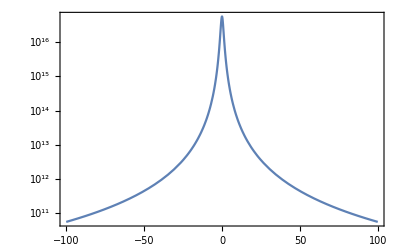

```mathematica
LogPlot[ρbh[x],{x,-100,100},Frame->True,PlotRange->All]
```

```mathematica
ρbhNorm[0]
```

3.05642×10^24

```mathematica
ρcf[x_]:= (3*c^2)/(8*π*g) *1/(ab^2*nb^2)*x^2*1/((1+x^2)^3)-ρbh[x] 
Plot[{ρcf[x]},{x,-1,1},Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
ρcf[0]
```

-5.63455×10^16

```mathematica
FullSimplify[(3*c^2)/(8*π*g) *1/(ab^2*nb^2)*x^2*1/((1+x^2)^3)-ρbh[x] ]
```

(3 c^2 x^2)/(8 ab^2 g nb^2 π (1+x^2)^3)+(-4 cini+x^2 (2+x^2) α)/(4 (1+x^2)^(3/2))

```mathematica
ρcfNorm[x_]:=ρcf[x]/ρcf[xini]
Plot[{ρcfNorm[x]},{x,-5,5},Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
D[ρcfNorm[x], x]
```

0.00542443 (-(3.64501×10^35 x^3)/((1+x^2)^4)+(1.215×10^35 x)/((1+x^2)^3)+(1.69036×10^17 x)/((1+x^2)^(5/2))-(-1.36633×10^-16 x-1.36633×10^-16 x^3)/((1+x^2)^(3/2))+(3 x (-6.83163×10^-17 x^2-3.41582×10^-17 x^4))/((1+x^2)^(5/2)))

```mathematica
NSolve[0.0054244338895610795 (-(3.6450106081425825*^35 x^3)/((1+x^2)^4)+(1.2150035360475275*^35 x)/((1+x^2)^3)+(1.6903642491439763*^17 x)/((1+x^2)^(5/2))-(-1.3663269110909684*^-16 x-1.3663269110909684*^-16 x^3)/((1+x^2)^(3/2))+(3 x (-6.831634555454842*^-17 x^2-3.415817277727421*^-17 x^4))/((1+x^2)^(5/2)))==0, x]
```

{{x→-7.25112×10^9-2.23166×10^10 ⅈ},{x→-7.25112×10^9+2.23166×10^10 ⅈ},{x→7.25112×10^9-2.23166×10^10 ⅈ},{x→7.25112×10^9+2.23166×10^10 ⅈ},{x→-2.34651×10^10},{x→2.34651×10^10},{x→-0.707107},{x→0.707107},{x→0.}}

```mathematica
NSolve[ρcfNorm[x]==0, x]
```

{{x→1.43869×10^10-1.04527×10^10 ⅈ},{x→1.43869×10^10+1.04527×10^10 ⅈ},{x→-1.43869×10^10-1.04527×10^10 ⅈ},{x→-1.43869×10^10+1.04527×10^10 ⅈ},{x→-9.63065×10^-10},{x→9.63065×10^-10}}

```mathematica
nb*9.630653306401809*^-10
```

0.0000211579

```mathematica
"rhocf.csv"

datosrhocfcerca=Table[{x,ρcf[x]},{x,-10^(-8),10^(-8), 10^(-11)}];
Export["rhocfcerca.csv",datosrhocfcerca]
```

rhocf.csv

rhocfcerca.csv

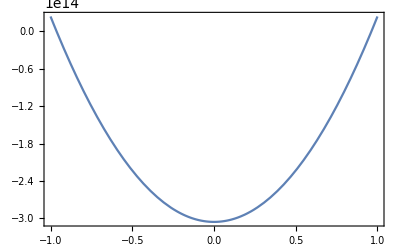

```mathematica
Plot[{ρcfNorm[x]},{x,-10^(-9),10^(-9)},Frame->True,PlotRange->All]
```

```mathematica
10^(-9)*nb
```

0.0000219693

```mathematica
NSolve[ρcf[x]==0, x]
```

{{x→1.43869×10^10-1.04527×10^10 ⅈ},{x→1.43869×10^10+1.04527×10^10 ⅈ},{x→-1.43869×10^10-1.04527×10^10 ⅈ},{x→-1.43869×10^10+1.04527×10^10 ⅈ},{x→-9.63065×10^-10},{x→9.63065×10^-10}}

```mathematica
NSolve[ρcfNorm[x]==0, x]
```

{{x→1.43869×10^10-1.04527×10^10 ⅈ},{x→1.43869×10^10+1.04527×10^10 ⅈ},{x→-1.43869×10^10-1.04527×10^10 ⅈ},{x→-1.43869×10^10+1.04527×10^10 ⅈ},{x→-9.63065×10^-10},{x→9.63065×10^-10}}

```mathematica
ρcfNorm[0]
```

-3.05642×10^14

```mathematica
dρcf[x_]:=1/4 x ((3 c^2 (1-2 x^2))/(ab^2 g nb^2 π (1+x^2)^4)+(12 cini+(4+2 x^2+x^4) α)/((1+x^2)^(5/2)))
```

```mathematica
NSolve[dρcf[x]==0, x]
```

{{x→7.25112×10^9-2.23166×10^10 ⅈ},{x→7.25112×10^9+2.23166×10^10 ⅈ},{x→-7.25112×10^9-2.23166×10^10 ⅈ},{x→-7.25112×10^9+2.23166×10^10 ⅈ},{x→-2.34651×10^10},{x→2.34651×10^10},{x→0.707107},{x→-0.707107},{x→0.}}

```mathematica
PCF[x_]:= 1/3*A*m0*c^2*ab*(1+x^2)^(1/2)-1/3*(1+x^2)/x*dρcf[x] - ρcf[x]
```

```mathematica
Plot[PCF[x], {x,-10,10},PlotRange->All ]
```

-Graphics-

```mathematica
PCF[x]
```

-(3 c^2 x^2)/(8 ab^2 g nb^2 π (1+x^2)^3)+1/3 A ab c^2 m0 √(1+x^2)+(-1/2 A ab c^2 m0 x^2-1/4 A ab c^2 m0 x^4)/((1+x^2)^(3/2))+(A ab c^2 m0 (xini^2/2+xini^4/4)+(1+xini^2)^(3/2) ρbhi)/((1+x^2)^(3/2))-1/12 (1+x^2) ((3 c^2 (1-2 x^2))/(ab^2 g nb^2 π (1+x^2)^4)+(A ab c^2 m0 (4+2 x^2+x^4)+12 (A ab c^2 m0 (xini^2/2+xini^4/4)+(1+xini^2)^(3/2) ρbhi))/((1+x^2)^(5/2)))

```mathematica
FullSimplify[PCF[x]]
```

(c^2 (-2+x^2))/(8 ab^2 g nb^2 π (1+x^2)^3)

```mathematica
Psimp[x_]:= (c^2 (-2+x^2))/(8 ab^2 g nb^2 π (1+x^2)^3)
```

```mathematica
Psimp[0]
```

-4.05001×10^34

```mathematica
Plot[Psimp[x], {x, -5, 5}]
```

-Graphics-

```mathematica
D[Psimp[x], x]
```

-(3 c^2 x (-2+x^2))/(4 ab^2 g nb^2 π (1+x^2)^4)+(c^2 x)/(4 ab^2 g nb^2 π (1+x^2)^3)

```mathematica
FullSimplify[-(3 c^2 x (-2+x^2))/(4 ab^2 g nb^2 π (1+x^2)^4)+(c^2 x)/(4 ab^2 g nb^2 π (1+x^2)^3)]
```

(c^2 x (7-2 x^2))/(4 ab^2 g nb^2 π (1+x^2)^4)

```mathematica
Plot[Psimp[x], {x, -2, 2},PlotRange->All ]
```

-Graphics-

```mathematica
pts:=Subdivide[-10,10,10000]
tabla:=Table[{x,Psimp[x]},{x,pts}]
Export["Pcf_lejos1.csv",tabla]
```

Pcf_lejos1.csv

```mathematica
pts:=Subdivide[-5,5,10000]
tabla:=Table[{x,Psimp[x]},{x,pts}]
Export["Pcf_lejos2.csv",tabla]
```

Pcf_lejos2.csv

```mathematica
Pini = Psimp[xini]
```

61.4503

```mathematica
PNorm[x_]:= Psimp[x]/Pini
```

```mathematica
Plot[PNorm[x], {x, -5, 5}]
```

-Graphics-

```mathematica
PNorm[0]
```

-6.59071×10^32

```mathematica
Clear[ab, nb, g, c, xini]
```

```mathematica
PNorm[x]
```

(c^2 (-2+x^2))/(8 ab^2 g nb^2 π (1+x^2)^3 PCF[xini])

```mathematica
PNorm[(√14)/2]
```

5.42445×10^30

```mathematica
pts:=Subdivide[-5,5,10000]
tabla:=Table[{x,PNorm[x]},{x,pts}]
Export["Pcf_lejos2.csv",tabla]
```

Pcf_lejos2.csv

```mathematica
NEC[x_]:= ρcf[x]+Psimp[x]
Plot[NEC[x], {x,-5,5},Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
pts:=Subdivide[-5,5,10000]
tabla:=Table[{x,NEC[x]},{x,pts}]
Export["NEC_mono.csv",tabla]
```

NEC_mono.csv

```mathematica
NEC[x_]:= ρcf[x]+Psimp[x]
```

```mathematica
NEC[x]
```

(3 c^2 x^2)/(8 ab^2 g nb^2 π (1+x^2)^3)+(c^2 (-2+x^2))/(8 ab^2 g nb^2 π (1+x^2)^3)-cini/((1+x^2)^(3/2))-(-(x^2 α)/2-(x^4 α)/4)/((1+x^2)^(3/2))

```mathematica
FullSimplify[NEC[x]]
```

1/4 ((c^2 (-1+2 x^2))/(ab^2 g nb^2 π (1+x^2)^3)+(-4 cini+x^2 (2+x^2) α)/((1+x^2)^(3/2)))

```mathematica
Solve[(c^2 (-1+2 x^2))/(ab^2 g nb^2 π (1+x^2)^3)+(-4 cini+x^2 (2+x^2) α)/((1+x^2)^(3/2))==0, x]
```

{{x→-1.5239×10^10-1.10718×10^10 ⅈ},{x→-1.5239×10^10+1.10718×10^10 ⅈ},{x→-0.707107},{x→0.707107},{x→1.5239×10^10-1.10718×10^10 ⅈ},{x→1.5239×10^10+1.10718×10^10 ⅈ}}

```mathematica
nb*0.7071067811865476
```

15534.6

```mathematica
SEC[x_]:= ρcf[x]+3*Psimp[x]
Plot[SEC[x], {x,-5,5}]
```

-Graphics-

```mathematica
pts:=Subdivide[-5,5,10000]
tabla:=Table[{x,SEC[x]},{x,pts}]
Export["SEC_mono.csv",tabla]
```

SEC_mono.csv

```mathematica
datosSEC=Table[If[x==0, Nothing,{x,SEC[x]}],{x,-5,5,0.0001}];
Export["SEC.csv",datosSEC]
```

SEC.csv

```mathematica
Solve[SEC[x]==0, x]
```

{{x→-1.65262×10^10+1.2007×10^10 ⅈ},{x→-1.65262×10^10-1.2007×10^10 ⅈ},{x→-1.},{x→1.},{x→1.65262×10^10+1.2007×10^10 ⅈ},{x→1.65262×10^10-1.2007×10^10 ⅈ}}

{{1.34733×10^8-1.65001×10^-8 ⅈ,4.52672×10^22-7.38889×10^6 ⅈ},{1.34677×10^8-4231.05 ⅈ,4.5242×10^22-1.89346×10^18 ⅈ},99996,{-1.00042×10^-10-3.14294×10^-15 ⅈ,3.11922×10^14+9.80759×10^-11 ⅈ},{-1/10000000000,3.11922×10^14}}
 |  |  |  |

dist.csv